### 1. Trafikflöde

#### Problem

Den här uppgiften går ut på och visa hur man kan använda linjära ekvationssystem för att studera trafikflödet genom ett trafiksystem. Trafiksystemet består av gator och korsningar där gatorna möts. Varje gata har ett visst flöde, som mäts i fordon per tidenhet. Vi skall beräkna trafikflödet för alla gatorna i trafiksystemet, givet flödet in till trafiksystemet.  Vi gör ett viktigt antagande: Trafikflödet bevaras i varje korsning. Det betyder att ett fordon som når en korsning måste fortsätta genom trafiksystemet. Ett positivt värde på flödet flyter i pilens riktning och ett negativt flöde flyter i motsatt riktning.

#### Uppgifter

Studera vägssystemet i figur 1. Siffrorna anger trafikflödena i fordon per timme. Alla vägar är enkelriktade och trafiken följer pilarnas riktning.

##### a) Är vårt antagande om att flödet bevaras giltigt? När kan antagandet vara felaktigt? “Trafikflödet bevaras i varje korsning” när ett fordon uppnår korsning bör komma fram genom trafiksystemet. Då sker trafiken så det är antagandet giltig i detta fall.Det blir fel när flödet kommer för någon anledning som ska hindras trafikflödet.

##### b) Vilka andra förenklingar har vi antagit? Enligt figure det är lätt att man vet vilket värde är positivt som hänvisar till pilens riktning. Däremot det negativa värdet hänvisar till motsats pilens riktning.

##### c) Ställ upp ekvationssystemet.

```mathematica
Quit[]
```

```mathematica
w+z==516;
z+y==340;
x+y==255;
```

##### d) Bestäm trafikflödet för vägsystemet.

```mathematica
p=Reduce[{w+z==516, z+y==340,x+y==255},{x,y,z,w}]
```

y==255-x&&z==85+x&&w==431-x

##### e) Om trafikflödet för en av x, y, z eller w begränsas till 100 fordon per timme på grund av vägarbete. Vad blir trafikflödet för de andra vägarna?

```mathematica
z=100;
```

```mathematica
Reduce[p]
```

y==240&&x==15&&w==416

```mathematica
Clear[z]
```

```mathematica
w=100;
```

```mathematica
Reduce[p]
```

z==416&&y==-76&&x==331

```mathematica
Clear[z,w]
```

```mathematica
y=100;
```

```mathematica
Reduce[p]
```

z==240&&x==155&&w==276

```mathematica
Clear[z,w,y]
```

```mathematica
Reduce[p]
```

y==340-z&&x==-85+z&&w==516-z

### 2. Kaniner

#### Problem

Leonardo av Pisa, även känd som Fibonacci (circa 1170-1250) skapade en av de äldsta matematiska modellerna av förökning. Han modellerade förökning av kaniner. Genom att modellera kaninpar kunde han undvika att ta hänsyn till individuella kaniner av olika kön. Modellen beskriver förökningen av kaniner från månad n=1 där p_n är antal kaniner vid månad n. När en kanin föds, så är den en unge under en månad och sedan förökar sig kaninparen varje månad. Antal kaniner kan då beskrivs av en differensekvation:

p_(n+2)=p_(n+1)+p_n

där vi antar att vi har bara ett kaninpar vid månad n=1, dvs intialvärdena är p_1=1 och p_2=1. Vilket betyder att p_3=2,  p_4=3 och p_5=5.

#### Uppgifter

##### a) Beräkna talföljden och rita en graf över den. - Eftersom kaniner förökar sig med ett bar på en månad. Vi antar att n är månader och börjar från månad 1, dvs n = 1. Dessutom antar vi att p_n är antal kaniner på en månad. Detta ger: Antal kaniner p_(n+2)=p_(n+1)+p_n , som ger att p_n=p_(n-1)+p_(n-2).

```mathematica
p[1]=1;
p[2]=1;
p[n_]:=p[n-1]+p[n-2]
```

```mathematica
kaninermängden=Table[p[n],{n,1,30}]
```

{1,1,2,3,5,8,13,21,34,55,89,144,233,377,610,987,1597,2584,4181,6765,10946,17711,28657,46368,75025,121393,196418,317811,514229,832040}

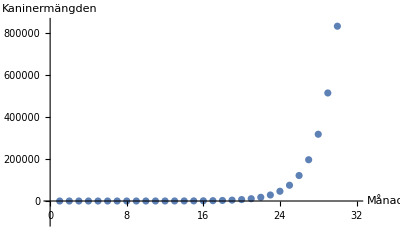

```mathematica
ListPlot[kaninermängden,AxesLabel-> {"Månad","Kaninermängden"}, PlotRange->{{0,32},{-100000,850000}}]
```

##### b) Undersök talföljden och diskutera tillväxtakten. - Talförljden visar en funktion som är exponential. I funktionen kan man se hur många kaniner kommer att existeras på den månaden som man vill undersöka. Om man exempelvis vill veta antal kaniner i månaden 20 då vissar detta till:

```mathematica
p[20]
```

6765

Dessutom kan vi märka att ökning börjar långsam men från och med månaden 25 börjar kaninermängden öka kraftig detta är take vare mängden blir större och större. Därutöver kan man veta antalet för en månad genom att addera de två sista månader.

```mathematica
tillväxtundersök=N [Table[p[n+1]/p[n],{n,1,30}]]
```

{1.,2.,1.5,1.66667,1.6,1.625,1.61538,1.61905,1.61765,1.61818,1.61798,1.61806,1.61803,1.61804,1.61803,1.61803,1.61803,1.61803,1.61803,1.61803,1.61803,1.61803,1.61803,1.61803,1.61803,1.61803,1.61803,1.61803,1.61803,1.61803}

##### c) Vilka begränsningar har modellen? Modellen kan vara lite svårt att stämma med verkligheten eftersom förökning kan inte alltid bli en hana och en hone. Det är stor möjlighet att kaninparet har fötts två honor eller tvärom två hanor och detta stämmer inte med antagande. Ytterligare begränsning är att modelle bort ser antal dödsfall som träffar under förökningen. Däremot kan det vara att kaninparet föder en kanin eller två eller tre, då kan mängden variera från månad till en annan.

##### d) Hur kan man förbättra modellen? De förbättrningar som man kan göra är att visa vilken kön kaninen har, antal dödsfall och antal kaniner som födds varje gång för det kan inte vara att paret föder bara två kaniner varje gång. .